```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ken_l/Documents/ads/mm-images

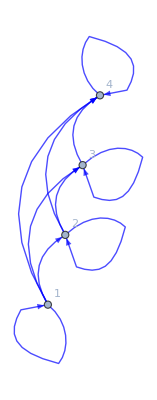

```mathematica
digraph=Map[DirectedEdge@@#&,(Tuples[{1,2,3,4},2]//Select[#,#[[1]]≤#[[2]]&]&)]//Graph[#,GraphLayout->"LinearEmbedding",VertexLabels->"Name",VertexSize->Small,VertexLabelStyle->Large,EdgeStyle->Blue,VertexCoordinates->Map[(#->{0.25#,#})&,Range[4]]]&
```

```mathematica
Export["fig-sol-6-2-1.png",digraph,"PNG"]
```

fig-sol-6-2-1.png

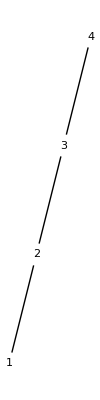

```mathematica
c=0.1;hasse=Graphics[{Map[Text[Style[ToString[#],Large],{0.25#,#}]&,Range[4]],Map[Line[{{0.25(#+c),#+c},{0.25(#+1-c),#+1-c}}]&,Range[3]]}]
```

```mathematica
Export["fig-sol-6-2-1_hasse.png",hasse,"PNG"]
```

fig-sol-6-2-1_hasse.png